# Quantum dot (2D harmonic oscillator)

Demonstration file of the Kohn-Sham density functional theory calculations with the SCE functional for a quantum dot in two dimensions.

Copyright (c) 2014, Christian B. Mendl
All rights reserved.
http://christian.mendl.net

This program is free software; you can redistribute it and/or
modify it under the terms of the Simplified BSD License
http://www.opensource.org/licenses/bsd-license.php

Reference:
  Christian B. Mendl, Francesc Malet, Paola Gori-Giorgi
  Wigner localization in quantum dots from Kohn-Sham density functional theory without symmetry breaking
  Physical Review B 89, 125106 (2014) [doi]
  (preprint arxiv:1311.6011)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
qdot2Dml=Install["mlink/"<>$SystemID<>"/qdot2D"];
```

## Common utility functions

```mathematica
?MLQuantumDotStep
```

MLQuantumDotStep[nelec_Integer, omega_Real, rho_List, dr_Real, nshpt_Integer, kBT_Real, phiStart_List, spinpol_Integer] performs a self-consistent field iteration step for a quantum dot model (2D harmonic oscillator) in the SCE formalism.

```mathematica
Polar0ToCoords[r_List,ϕ_List]:=Table[r⟦i⟧{Cos[ϕ⟦i⟧],Sin[ϕ⟦i⟧]},{i,Length[r]}]
```

```mathematica
PerformSCFIteration[numEl_,ω_,spinpol_,kBT_,λ_,initsc_:1/3]:=Module[{λr=If[NumberQ[λ],ConstantArray[λ,Subscript[maxiter, numEl,ω]],λ],kBTlist=If[NumberQ[kBT],ConstantArray[kBT,Subscript[maxiter, numEl,ω]],kBT]},
Subscript[ρ, numEl,ω,spinpol,0]=N[(initsc ω) Subscript[ρ, 0][numEl,(initsc ω)^(1/2)#]&/@Subscript[ρrgrid, numEl,ω]];
(If[Mod[#,10]==0,Print["iteration: ",#]];
{Subscript[ρ1, numEl,ω,spinpol,#],Subscript[levels, numEl,ω,spinpol,#],Subscript[v, numEl,ω,spinpol,#],Subscript[dv, numEl,ω,spinpol,#],Subscript[a, numEl,ω,spinpol,#],Subscript[f, numEl,ω,spinpol,#],Subscript[ϕ, numEl,ω,spinpol,#],Subscript[g, numEl,ω,spinpol,#]}=MLQuantumDotStep[numEl,N[ω],Subscript[ρ, numEl,ω,spinpol,#-1],N[Subscript[ρrgrid, numEl,ω]⟦2⟧],Subscript[n, shpt,numEl,ω],kBTlist⟦#⟧,N[Subscript[ϕstart, numEl,ω,spinpol]],If[spinpol===npol,0,1]];
Subscript[c, numEl,ω,spinpol,#]=Transpose[MapThread[Polar0ToCoords[#1,#2]&,{Subscript[f, numEl,ω,spinpol,#],Subscript[ϕ, numEl,ω,spinpol,#]}]];
Subscript[ρ, numEl,ω,spinpol,#]=λr⟦#⟧ Subscript[ρ1, numEl,ω,spinpol,#]+(1-λr⟦#⟧)Subscript[ρ, numEl,ω,spinpol,#-1])&/@Range[Subscript[maxiter, numEl,ω]]];
```

```mathematica
CalculateWignerSeitzRadius[numEl_,ρ_,rmax_]:=(π 1/numEl NIntegrate[ρ[r]^2 2π r,{r,0,rmax}])^(-1/2)
```

```mathematica
PlotRadialComotionFunctions[numEl_,ω_,spinpol_]:=Module[{maxit=Subscript[maxiter, numEl,ω]},
ListLinePlot[Transpose[{Subscript[f, numEl,ω,spinpol,maxit]⟦;;,1⟧,#}]&/@Transpose[Subscript[f, numEl,ω,spinpol,maxit]],PlotRange->KroneckerProduct[{1,1},{0,Subscript[f, numEl,ω,spinpol,maxit]⟦-1,1⟧}],AspectRatio->1,AxesLabel->{"r","f_i(r)"},PlotLegends->("\!\(\*SubscriptBox[\(f\), \("<>ToString[#]<>"\)]\)(r)"&/@Range[numEl]),ImageSize->Small,PlotStyle->{Blue,Red,Green,Orange,Magenta,Cyan,Brown}]]
```

```mathematica
PlotComotionFunctions[numEl_,ω_,spinpol_,range_]:=Module[{maxit=Subscript[maxiter, numEl,ω]},
GraphicsRow[Table[Show[ListPlot[Subscript[c, numEl,ω,spinpol,maxit]⟦;;,(i-1)Subscript[n, shpt,numEl,ω]+1;;i Subscript[n, shpt,numEl,ω]⟧,PlotRange->{{-range,range},{-range,range}},AspectRatio->1,PlotStyle->{Blue,Red,Green,Orange,Magenta,Cyan,Brown}],Graphics[Locator/@Select[Subscript[c, numEl,ω,spinpol,maxit]⟦;;,(i-1)Subscript[n, shpt,numEl,ω]+1⟧,NumericQ[First[#]]&]],Graphics[{Gray,Circle[{0,0},#]&/@Subscript[a, numEl,ω,spinpol,maxit]⟦1;;-2⟧}]],{i,numEl}],ImageSize->200numEl]]
```

```mathematica
CheckDensityNormalization[numEl_,ω_,spinpol_]:=(Subscript[ρ, numEl,ω,spinpol,#] 2π Subscript[ρrgrid, numEl,ω])⟦1;;-2⟧.Differences[Subscript[ρrgrid, numEl,ω]]-numEl&/@Range[0,Subscript[maxiter, numEl,ω],10]
```

```mathematica
PlotLabelString[numEl_,ω_]:="N="<>ToString[numEl]<>", ω="<>ToString[N[ω]]
```

```mathematica
(* check total energy convergence (sum of Kohn-Sham eigenvalues) *)
PlotEnergyConvergence[numEl_,ω_]:=Module[{en},en=Table[Table[Total[First[#]Last[#]&/@Subscript[levels, numEl,ω,{npol,pol}⟦i⟧,iter]],{iter,Subscript[maxiter, numEl,ω]}],{i,2}];ListLogPlot[Transpose[{Range[Subscript[maxiter, numEl,ω]],Abs[#-Last[#]]}]&/@en,PlotLegends->LineLegend[{"unpol.","pol."}],(*PlotStyle->{Blue,Magenta},*)ImageSize->Small,Joined->True,AxesLabel->{"iter","ΔE_tot"},PlotLabel->PlotLabelString[numEl,ω]]]
```

```mathematica
PlotSelfConsistentDensity[numEl_,ω_,yticks_:Automatic]:=Module[{maxit=Subscript[maxiter, numEl,ω]},Show[ListLinePlot[{Transpose[{Subscript[ρrgrid, numEl,ω],Subscript[ρ, numEl,ω,npol,maxit]}],Transpose[{Subscript[ρrgrid, numEl,ω],Subscript[ρ, numEl,ω,pol,maxit]}]},AxesLabel->{"r","ρ(r)"},PlotRange->All,Ticks->{Automatic,yticks},PlotLegends->{"unpol.","pol."},ImageSize->Small]]]
```

```mathematica
PlotKantorovichPotential[numEl_,ω_]:=Module[{maxit=Subscript[maxiter, numEl,ω]},Show[ListLinePlot[Table[Transpose[{Subscript[f, numEl,ω,{npol,pol}⟦i⟧,maxit]⟦;;,1⟧,Subscript[v, numEl,ω,{npol,pol}⟦i⟧,maxit]}],{i,2}],(*PlotStyle->{Blue,Lighter[Blue]},*)AxesLabel->{"r","v(r)"},AxesOrigin->{0,0},PlotLegends->{"unpol.","pol."},ImageSize->Small,PlotRange->{All,{0,1.5Max[Subscript[v, numEl,ω,npol,maxit]⟦1⟧,Subscript[v, numEl,ω,pol,maxit]⟦1⟧]}}],Plot[(numEl-1)/r,{r,0,Max[Subscript[f, numEl,ω,npol,maxit]⟦-1,1⟧,Subscript[f, numEl,ω,pol,maxit]⟦-1,1⟧]},PlotStyle->{Gray,Dashed}]]]
```

```mathematica
(* sum of Kantorovich and confinement potential *)
PlotKantorovichPlusConfinementPotential[numEl_,ω_]:=
Module[{maxit=Subscript[maxiter, numEl,ω]},ListLinePlot[Table[Transpose[{Subscript[f, numEl,ω,{npol,pol}⟦i⟧,maxit]⟦;;,1⟧,Subscript[v, numEl,ω,{npol,pol}⟦i⟧,maxit]+1/2 ω^2(Subscript[f, numEl,ω,{npol,pol}⟦i⟧,maxit]⟦;;,1⟧)^2}],{i,2}],AxesLabel->{"r","v(r)+1/2ω^2r^2"},PlotLegends->{"unpol.","pol."},PlotRange->All,ImageSize->Small]]
```

```mathematica
PrintWignerSeitzRadius[numEl_,ω_]:=Module[{maxit=Subscript[maxiter, numEl,ω]},Table[CalculateWignerSeitzRadius[numEl,Interpolation[Transpose[{Subscript[ρrgrid, numEl,ω],Subscript[ρ, numEl,ω,{npol,pol}⟦i⟧,maxit]}]],Last[Subscript[ρrgrid, numEl,ω]]],{i,2}]]
```

```mathematica
(* 'g' function (E_pot), interaction between the electrons and the SCE potential *)
PlotGFunction[numEl_,ω_]:=
Block[{maxit=Subscript[maxiter, numEl,ω],data,dpol},GraphicsGrid[Table[data=Transpose[{Subscript[f, numEl,ω,{npol,pol}⟦i⟧,maxit]⟦;;,1⟧,Subscript[g, numEl,ω,{npol,pol}⟦i⟧,maxit]}];{ListLinePlot[data,AxesLabel->{"r","g[r]"},PlotStyle->Blue,Mesh->All,PlotRange->All,PlotLabel->PlotLabelString[numEl,ω]<>{", spin-unpol.",", spin-pol."}⟦i⟧],ListLinePlot[data,AxesLabel->{"r","g[r]"},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->Automatic,PlotLabel->PlotLabelString[numEl,ω]<>{", spin-unpol.",", spin-pol."}⟦i⟧]},{i,2}]]]
```

```mathematica
EnergyLevelTable[numEl_,ω_,p_,usec_]:=Module[{lev,c,maxit},maxit=Subscript[maxiter, numEl,ω];lev=Subscript[levels, numEl,ω,p,maxit];c=If[usec,Median[Subscript[g, numEl,ω,p,maxit]]/numEl,0];Join[{{If[p===npol,"spin-unpolarized","spin-polarized"]<>", C="<>ToString[c],},{"en","n","m","occupancy"}},{#⟦1⟧+c,#⟦2,1⟧,#⟦2,2⟧,#⟦3⟧}&/@lev,{{Total[(First[#]+c)Last[#]&/@lev],"total energy",}}]]
```

```mathematica
PrintEnergyLevels[numEl_,ω_]:=Module[{tnpol0,tnpol1,tpol0,tpol1},Grid[Join[{{"N="<>ToString[numEl]<>", ω="<>ToString[N[ω]],}},tnpol0=EnergyLevelTable[numEl,ω,npol,False],
tnpol1=EnergyLevelTable[numEl,ω,npol,True],
tpol0=EnergyLevelTable[numEl,ω,pol,False],
tpol1=EnergyLevelTable[numEl,ω,pol,True]],Dividers->{{2->Black,3->Black,4->Black},{2->{Thick,Black},(Length[tnpol0]+1)->{Dashed,Black},(Length[tnpol0]+2)->Black,(Length[tnpol0]+Length[tnpol1]+1)->{Dashed,Black},(Length[tnpol0]+Length[tnpol1]+2)->{Thick,Black},(-2-Length[tpol1])->{Dashed,Black},(-1-Length[tpol1])->Black,-2->{Dashed,Black},-1->{Thick,Black}}}]]
```

## SCF iterations, ω=0.001

### N=5

```mathematica
(* number of iterations *)
Subscript[maxiter, 5,1/1000]=70;
```

```mathematica
(* radial grid for density *)
Subscript[ρrgrid, 5,1/1000]=Range[0,250,1/10];
Length[%]
```

2501

```mathematica
(* number of discretization points for each subshell *)
Subscript[n, shpt,5,1/1000]=256;
```

```mathematica
(* initial density Subscript[ρ, 0] *)
Subscript[ρ, 0][numEl_,r_]:=Module[{a=3/2},numEl/(π(Exp[-a^2]+a √π (1+Erf[a])))Exp[-(r-a)^2]]
```

```mathematica
(* check normalization *)
Integrate[Subscript[ρ, 0][1,r]2π r,{r,0,∞}]
Integrate[ω Subscript[ρ, 0][1,ω^(1/2)r]2π r,{r,0,∞},Assumptions:>{ω>0}]
```

1

1

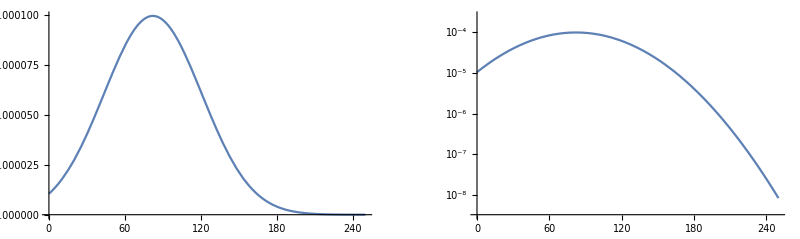

```mathematica
(* show rescaled initial density *)
Block[{numEl=5,ω=1/1000},
GraphicsRow[{Plot[(ω/3)Subscript[ρ, 0][numEl,(ω/3)^(1/2)r],{r,0,250}],LogPlot[(ω/3) Subscript[ρ, 0][numEl,(ω/3)^(1/2)r],{r,0,250}]}]]
```

#### spin-unpolarized

```mathematica
(* initial starting angles for optimization *)
Subscript[ϕstart, 5,1/1000,npol]={0,2.4,-2.5,-1.1,1.1};
```

```mathematica
(* perform SCF iteration *)
PerformSCFIteration[5,1/1000,npol,0.(*Subscript[k, B] T*),0.1(*mixing parameter*)];
```

MLQuantumDotStep::Iteration: angle optimization iteration canceled, error message: "iteration is not making progress towards solution"

General::stop: Further output of MLQuantumDotStep :: Iteration will be suppressed during this calculation.

iteration: 10

iteration: 20

iteration: 30

iteration: 40

iteration: 50

iteration: 60

iteration: 70

```mathematica
(* example: co-motion functions at iteration 42 *)
Subscript[f, 5,1/1000,npol,42]⟦96,;;⟧
```

{72.3892,99.4214,109.535,126.206,139.222}

```mathematica
(* example: shell radii at iteration 42 *)
Subscript[a, 5,1/1000,npol,42]
```

{0.,88.9253,104.644,117.614,132.043,∞}

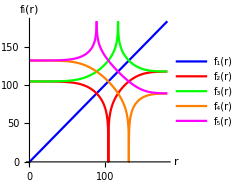

```mathematica
PlotRadialComotionFunctions[5,1/1000,npol]
```

```mathematica
PlotComotionFunctions[5,1/1000,npol,200]
```

-Graphics-

```mathematica
(* check normalization *)
CheckDensityNormalization[5,1/1000,npol]
```

{-0.00011559,-0.0000416887,-0.0000162843,-7.37019×10^-6,-4.22897×10^-6,-3.11841×10^-6,-2.7255×10^-6,-2.58677×10^-6}

#### spin-polarized

```mathematica
(* initial starting angles for optimization *)
Subscript[ϕstart, 5,1/1000,pol]={0,2.4,-2.5,-1.1,1.1};
```

```mathematica
(* perform SCF iteration *)
PerformSCFIteration[5,1/1000,pol,0.0(*Subscript[k, B] T*),0.1(*mixing parameter*)];
```

MLQuantumDotStep::Iteration: angle optimization iteration canceled, error message: "iteration is not making progress towards solution"

General::stop: Further output of MLQuantumDotStep :: Iteration will be suppressed during this calculation.

iteration: 10

iteration: 20

iteration: 30

iteration: 40

iteration: 50

iteration: 60

iteration: 70

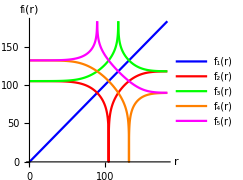

```mathematica
PlotRadialComotionFunctions[5,1/1000,pol]
```

```mathematica
PlotComotionFunctions[5,1/1000,pol,200]
```

-Graphics-

```mathematica
(* check normalization *)
CheckDensityNormalization[5,1/1000,pol]
```

{-0.00011559,-0.0000426828,-0.0000181524,-9.47161×10^-6,-6.38631×10^-6,-5.29108×10^-6,-4.901×10^-6,-4.76176×10^-6}

#### visualize results

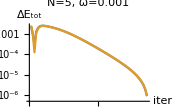

```mathematica
(* check total energy convergence (sum of Kohn-Sham eigenvalues) *)
PlotEnergyConvergence[5,1/1000]
```

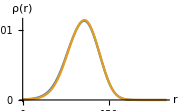

```mathematica
PlotSelfConsistentDensity[5,1/1000,{0,0.00005,0.0001}]
```

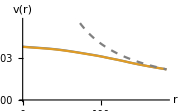

```mathematica
PlotKantorovichPotential[5,1/1000]
```

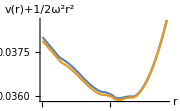

```mathematica
PlotKantorovichPlusConfinementPotential[5,1/1000]
```

```mathematica
(* Wigner-Seitz radius Subscript[r, s] *)
PrintWignerSeitzRadius[5,1/1000]
```

{62.3424,62.0487}

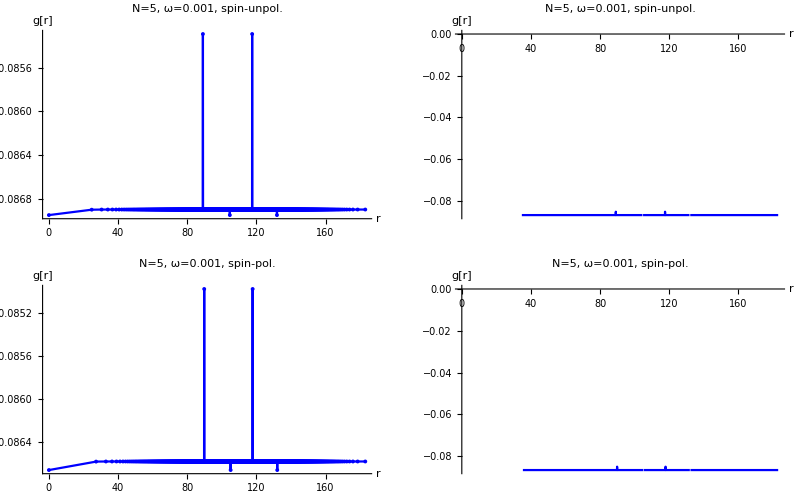

```mathematica
(* 'g' function (E_pot), interaction between the electrons and the SCE potential, should be constant *)
PlotGFunction[5,1/1000]
```

```mathematica
PrintEnergyLevels[5,1/1000]
```

N=5, ω=0.001 |  |  | 
spin-unpolarized, C=0 |  |  | 
en | n | m | occupancy
0.0363225 | 0 | 0 | 2.
0.036374 | 0 | 1 | 3.
0.181767 | total energy |  | 
spin-unpolarized, C=-0.0173799 |  |  | 
en | n | m | occupancy
0.0189425 | 0 | 0 | 2.
0.0189941 | 0 | 1 | 3.
0.0948673 | total energy |  | 
spin-polarized, C=0 |  |  | 
en | n | m | occupancy
0.0362569 | 0 | 0 | 1.
0.036311 | 0 | 1 | 2.
0.0364558 | 0 | 2 | 2.
0.18179 | total energy |  | 
spin-polarized, C=-0.0173173 |  |  | 
en | n | m | occupancy
0.0189396 | 0 | 0 | 1.
0.0189938 | 0 | 1 | 2.
0.0191385 | 0 | 2 | 2.
0.0952042 | total energy |  |

## Clean up

```mathematica
Uninstall[qdot2Dml];
```